```mathematica
{vsol,ysol}=NDSolveValue[{Ri*v'[t]+v[t]/Ce+pex==pset,Ree*y'[t]+y[t]/Ce+pex==pp,v[0]==0,y[2]==1.03},{v,y},{t,0,4}]
```

{InterpolatingFunction[{{0., 4.}}, <>],InterpolatingFunction[{{0., 4.}}, <>]}

```mathematica
Ri=16.41;
Ree=16.41;
Ce=0.1;
pex=4.85;
pset=20;
pp=0;
```

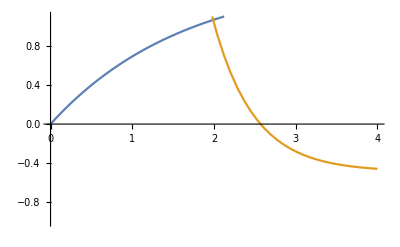

```mathematica
Plot[{vsol[t],ysol[t]},{t,0,4},PlotRange->{-1,1.1}]
```

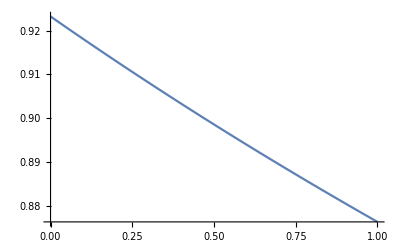

```mathematica
Plot[√((Ri/(2x))^2+(pset-pex)/x)-Ri/(2x),{x,0,1}]
```

```mathematica
A=ⅇ^(2/(Ce Ri));
B=ⅇ^(4/(Ce Ri));
```

```mathematica
pex
```

4.85

```mathematica
De=ⅇ^(-2/(Ce*Ri))
```

0.295594

```mathematica
pex+1.03/(De(A-1) Ce)
```

19.4722

```mathematica
pex
```

4.85